Predicting pathogenicity from Viral Genomic sequences

Karthik Gangavarapu

Mark Boyer

The Scripps Research Institute

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: The goal of the project is to train Artificial Neural Networks to identify pathogenic viral species from genomic sequences. Viral genomic sequences will be extracted from the NCBI Reference Sequence Database(RefSeq) and the pathogen information will be extracted from the Human Disease Ontology[1]. These labelled viral genomes will then be used to train and test a Convolutional Neural Network.

SUMMARY OF WORK: Fasta files from Refseq were downloaded and labelled using the pathogen information obtained from a locally hosted Neo4j instance of the Human Disease Ontology. This data was then uploaded to the Wolfram Data Repository[link]. Viral sequences were then broken into chunks of 1000 bps and labeled as being pathogenic or non-pathogenic. This labelled data was then used to train and test a Convolutional Neural Network[2].

RESULTS AND FUTURE  WORK: Experiments with multiple configurations of Convolutional Neural Networks were conducted. The best performing network among these was able to attain an accuracy of 76% on a test set. Going forward it would be necessary to increase the training and test set size. There seem to be promising results using hybrid network configurations[3]. Instead of chunking down the sequences into 1000 bps, they can be converted into a sparse genome-feature[4] matrix at the preprocessing stage.

References:
1. Umarov et al. Recognition of prokaryotic and eukaryotic promoters using convolutional deep learning neural networks. PLOS one. Feb 3, 2017.
2. Quang et al. DanQ: a hybrid convolutional and recurrent deep neural network for quantifying the function of DNA sequences. Nucleic Acids Res (2016) 44 (11). 
3. Wen et al. k-mer Sparse matrix model for genetic sequence and its applications in sequence comparison. Journal of Theoretical Biology (2016) 145-150.
4. Kibbe et al.Disease Ontology 2015 update: an expanded and updated database of human diseases for linking biomedical knowledge through disease data. Nucleic Acids Research 2014; Oct 27

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

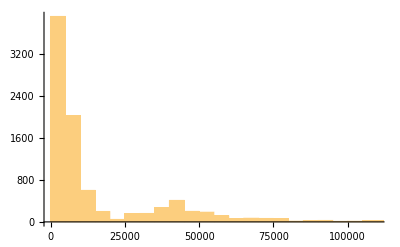

Dataset[<>]

```mathematica
With[{ds=ResourceData["749327c2-fbd2-42db-b39c-597a7773057c"]},
Print[Histogram[StringLength/@ds[All,"Genome"]]];
g=Select[ds,StringContainsQ[#Name,"ebola"]&]
]
```

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

Code

Provide one of:

Link to the GitHub

Explicit code

Written Content / Lesson Plans

Conclusions in Detail

All Visualizations

Data Sources Links/References

Future Directions

Background Info Links/References

Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```